```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Define stuff

```mathematica
JEVMaxwellianPhiBar[phiBar,RB,Tm,nm]
```

0.0000268059 nm (2+phiBar-ⅇ^(-phiBar/(-1+RB)) (phiBar+2 (1-1/RB))) RB Tm^(3/2)

```mathematica
JEVKappaPhiBar[phiBar,RB,Tm,nm,kappa]
```

1/((-2+kappa) (-1+kappa) Gamma[-1/2+kappa])0.0000268059 (1-3/(2 kappa))^(3/2) √kappa nm (2+((-2+kappa) phiBar)/(-3/2+kappa)-((-2+kappa)/(-1+kappa)+((-2+kappa) phiBar)/(-3/2+kappa)) (1+kappa/((-1+kappa) (-1+RB))) (1+phiBar/((-3/2+kappa) (-1+RB)))^(1-kappa) (1-1/RB)-(1+(1+kappa/(-1+RB))/(-1+kappa)) (1+phiBar/((-3/2+kappa) (-1+RB)))^(2-kappa) (1-1/RB)^2) RB Tm^(3/2) Gamma[1+kappa]

```mathematica
JEVratPhiBar[phiBar_,RB_,Tm_,kappa_]:=JEVKappaPhiBar[phiBar,RB,Tm,nm,kappa]/JEVMaxwellianPhiBar[phiBar,RB,Tm,nm]
JEVrat[pot_,RB_,Tm_,kappa_]:=JEVKappa[pot,RB,Tm,nm,kappa]/JEVMaxwellian[pot,RB,Tm,nm]
```

## Define cases

```mathematica
TmLow=50;
TmHigh = 500;
RBLow = 30;
RBHigh = 300;
```

First case:  Low temp, nearby source

```mathematica
TLowRBLowTable = Table[JEVrat[pot,RBLow,TmLow,kapVal],{kapVal,{1.7,2.2,3.,10.}}];
TLowRBHighTable = Table[JEVrat[pot,RBHigh,TmLow,kapVal],{kapVal,{1.7,2.2,3.,10.}}];
THighRBHighTable = Table[JEVrat[pot,RBHigh,TmHigh,kapVal],{kapVal,{1.7,2.2,3.,10.}}];
THighRBLowTable = Table[JEVrat[pot,RBLow,TmHigh,kapVal],{kapVal,{1.7,2.2,3.,10.}}];
```

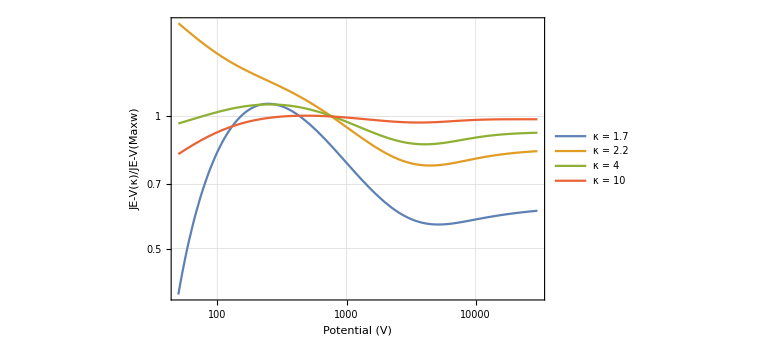

```mathematica
LogLogPlot[TLowRBLowTable,{pot,50,30000},PlotLegends->{"κ = 1.7","κ = 2.2","κ = 4","κ = 10"},
Frame->True,GridLines->Automatic,
FrameLabel->{{"JE-V(κ)/JE-V(Maxw)",""},
{"Potential (V)",
Text[Style["T = 50 eV, RB = 30",FontSize->20]]}},ImageSize->Large]
```

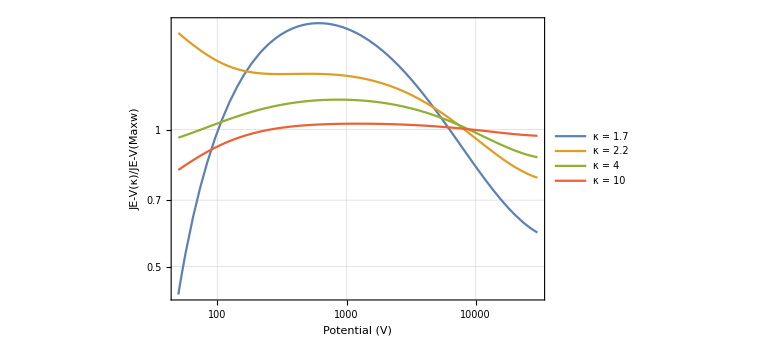

```mathematica
LogLogPlot[TLowRBHighTable,{pot,50,30000},PlotLegends->{"κ = 1.7","κ = 2.2","κ = 4","κ = 10"},
Frame->True,GridLines->Automatic,
FrameLabel->{{"JE-V(κ)/JE-V(Maxw)",""},
{"Potential (V)",
Text[Style["T = 50 eV, RB = 300",FontSize->20]]}},ImageSize->Large]
```

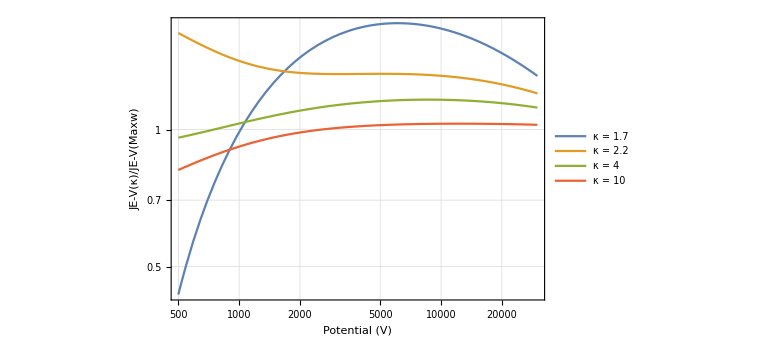

```mathematica
LogLogPlot[THighRBHighTable,{pot,500,30000},PlotLegends->{"κ = 1.7","κ = 2.2","κ = 4","κ = 10"},
Frame->True,GridLines->Automatic,
FrameLabel->{{"JE-V(κ)/JE-V(Maxw)",""},
{"Potential (V)",
Text[Style["T = 500 eV, RB = 300",FontSize->20]]}},ImageSize->Large]
```

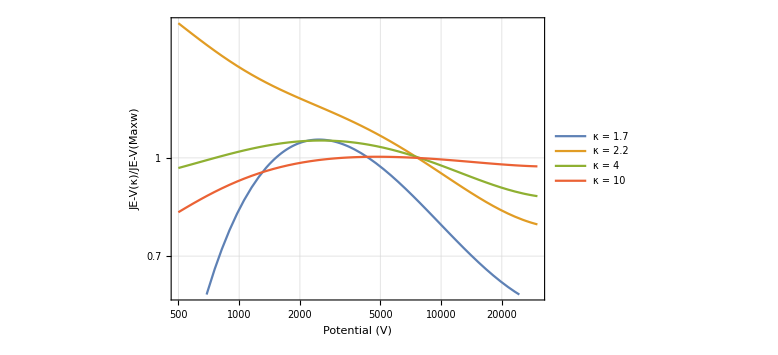

```mathematica
LogLogPlot[THighRBLowTable,{pot,500,30000},PlotLegends->{"κ = 1.7","κ = 2.2","κ = 4","κ = 10"},
Frame->True,GridLines->Automatic,
FrameLabel->{{"JE-V(κ)/JE-V(Maxw)",""},
{"Potential (V)",
Text[Style["T = 500 eV, RB = 30",FontSize->20]]}},ImageSize->Large]
```

```mathematica
JEVMaxwellianPhiBar::usage="
JEVMaxwellianPhiBar[phiBar_,RB_,Tm_,nm_]
```